```mathematica
S[α_]:=({{1, 0}, {α, 1}}); A=({{0, -ⅈ}, {-ⅈ, 0}}); W[a_]:=({{Exp[a], 0}, {0, Exp[-a]}});
Q[a_,b_,x_]:=Function[z,FullSimplify[(b-a^2/4-D[a,x]/2)/.x->z]];
U[Q_,g_,x_]:=Function[z,FullSimplify[(Q[g] D[g,x]^2-3/4(D[g,{x,2}]/D[g,x])^2+1/2(D[g,{x,3}]/D[g,x]))/.x->z]];
```

{{x→-1.10464},{x→0.30732+0.764532 ⅈ},{x→0.30732-0.764532 ⅈ}}

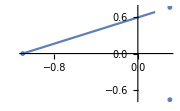
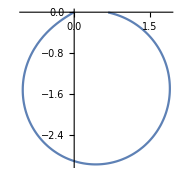
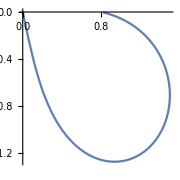

0.346538+1.66464 ⅈ

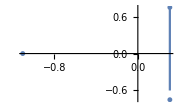
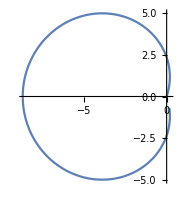
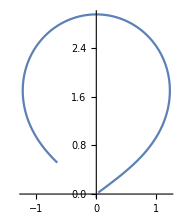

-6.82565×10^-13+2.11212 ⅈ

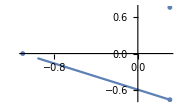
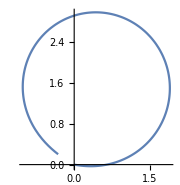
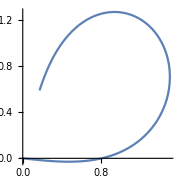

0.346538-1.66464 ⅈ

```mathematica
δ=0.7;Q=Function[x,-(x+δ^2+3/(4 x^2))] ;
zeros=NSolve[Q[x]==0,x]

ab=Function[t,(x/.zeros[[1]])+((x/.zeros[[2]])-(x/.zeros[[1]]))t];
abVal=Function[t,√Q[ab[t]]];

Show[ListPlot[Table[{Re[x/.zeros[[i]]],Im[x/.zeros[[i]]]},{i,1,Length[zeros]}]],ParametricPlot[(ab[t])//{Re[#],Im[#]}&,{t,0,0.9}],ImageSize->Small];
ParametricPlot[Q[ab[t]]//{Re[#],Im[#]}&,{t,0,0.9},PlotRange->Full,ImageSize->Small];
ParametricPlot[abVal[t]//{Re[#],Im[#]}&,{t,0,0.9},PlotRange->Full,ImageSize->Small];
Row[{%%%,%%,%}]
NIntegrate[ⅈ(abVal[t]ab'[t]),{t,0,1}]

bc=Function[t,(x/.zeros[[2]])+((x/.zeros[[3]])-(x/.zeros[[2]]))t];
bcVal=Function[t,Piecewise[{{√Q[bc[t]],Im[Q[bc[t]]]>=0},{-√Q[bc[t]],Im[Q[bc[t]]]<0}}]];

Show[ListPlot[Table[{Re[x/.zeros[[i]]],Im[x/.zeros[[i]]]},{i,1,Length[zeros]}]],ParametricPlot[(bc[t])//{Re[#],Im[#]}&,{t,0,0.9}],ImageSize->Small];
ParametricPlot[Q[bc[t]]//{Re[#],Im[#]}&,{t,0,0.9},PlotRange->Full,ImageSize->Small];
ParametricPlot[bcVal[t]//{Re[#],Im[#]}&,{t,0,0.9},PlotRange->Full,ImageSize->Small];
Row[{%%%,%%,%}]
NIntegrate[ⅈ(bcVal[t]bc'[t]),{t,0,1}]

ca=Function[t,(x/.zeros[[3]])+((x/.zeros[[1]])-(x/.zeros[[3]]))t];
caVal=Function[t,√Q[ca[t]]];

Show[ListPlot[Table[{Re[x/.zeros[[i]]],Im[x/.zeros[[i]]]},{i,1,Length[zeros]}]],ParametricPlot[(ca[t])//{Re[#],Im[#]}&,{t,0,0.9}],ImageSize->Small];
ParametricPlot[Q[ca[t]]//{Re[#],Im[#]}&,{t,0,0.9},PlotRange->Full,ImageSize->Small];
ParametricPlot[caVal[t]//{Re[#],Im[#]}&,{t,0,0.9},PlotRange->Full,ImageSize->Small];
Row[{%%%,%%,%}]
NIntegrate[ⅈ(caVal[t]ca'[t]),{t,0,1}]
```

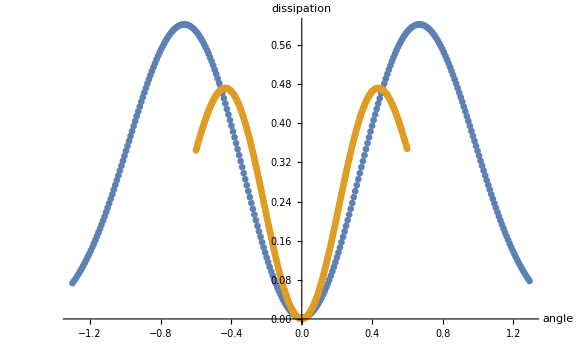

```mathematica
Dissipation={};
begining=-1.3;end=1.3;nstep=300;
ProgressIndicator[Dynamic[(δ-begining)/(end-begining)]]

δ=0;
Q=Function[x,-(x+δ^2+3/(4 x^2))];zeros=NSolve[Q[x]==0,x];
ca=Function[t,(x/.zeros[[3]])+((x/.zeros[[1]])-(x/.zeros[[3]]))t];
caVal=Function[t,√Q[ca[t]]];
CA0=NIntegrate[ⅈ(caVal[t]ca'[t]),{t,0,1}];

For[δ=begining,δ<end,δ+=(end-begining)/nstep,
Q=Function[x,-(x+δ^2+3/(4 x^2))];
zeros=NSolve[Q[x]==0,x];
ca=Function[t,(x/.zeros[[3]])+((x/.zeros[[1]])-(x/.zeros[[3]]))t];
caVal=Function[t,√Q[ca[t]]];
CA=NIntegrate[ⅈ(caVal[t]ca'[t]),{t,0,1}];
(*Amp=FullSimplify[S[-ⅈ].W[CA].S[2ⅈ*Exp[2CA0]].({{1}, {0}})];*)
Amp=FullSimplify[S[1].W[CA].S[Stokes⟦1,2⟧].({{1}, {0}})];
Dissipation=Append[Dissipation,{δ,1-Abs[(Amp[[2]][[1]])/(Amp[[1]][[1]])]^2}];
]; Clear[Amp,δ];
ListPlot[{Dissipation,δDissipation},PlotRange->Full,AxesLabel->{angle,dissipation},ImageSize->Large]
```

{{x→-0.908793},{x→0.454396+0.786635 ⅈ},{x→0.454396-0.786635 ⅈ},{x→-1.64354×10^-7+0.0185216 ⅈ},{x→-1.64354×10^-7-0.0185216 ⅈ},{x→0.00311717},{x→-0.00311717}}

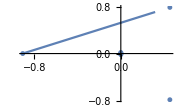
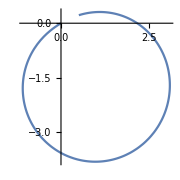
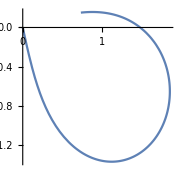

0.000257496+1.81395 ⅈ

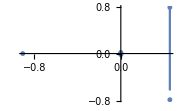
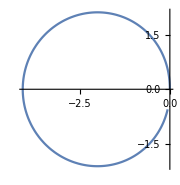
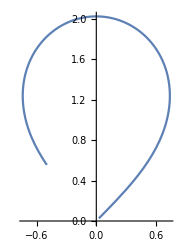

-2.64719×10^-15+1.8135 ⅈ

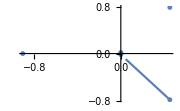
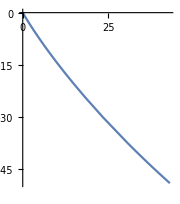
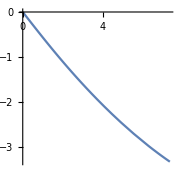

-2.85634-0.453599 ⅈ

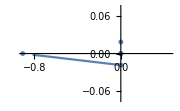
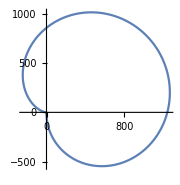
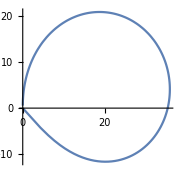

2.8566-1.36035 ⅈ

```mathematica
δ=0;β=0.01; Q=Function[x,(-4 x^7+12 x^5 β^2+β^4-12 x^3 β^4+4 x β^6-4 x^6 δ^2+x^4 (-3+8 β δ (1+β δ))-2 x^2 β^2 (5+2 β δ (2+β δ)))/(4 (x^3-x β^2)^2)];zeros=NSolve[Q[x]==0,x]
ab=Function[t,(x/.zeros[[1]])+((x/.zeros[[2]])-(x/.zeros[[1]]))t];
abVal=Function[t,√Q[ab[t]]];

Show[ListPlot[Table[{Re[x/.zeros[[i]]],Im[x/.zeros[[i]]]},{i,1,Length[zeros]}],PlotRange->Full],ParametricPlot[(ab[t])//{Re[#],Im[#]}&,{t,0,0.9}],ImageSize->Small];
ParametricPlot[Q[ab[t]]//{Re[#],Im[#]}&,{t,0,0.9},PlotRange->Full,ImageSize->Small];
ParametricPlot[abVal[t]//{Re[#],Im[#]}&,{t,0,0.9},PlotRange->Full,ImageSize->Small];
Row[{%%%,%%,%}]
NIntegrate[ⅈ(abVal[t]ab'[t]),{t,0,1}]

bc=Function[t,(x/.zeros[[2]])+((x/.zeros[[3]])-(x/.zeros[[2]]))t];
bcVal=Function[t,Piecewise[{{√Q[bc[t]],Im[Q[bc[t]]]>=0},{-√Q[bc[t]],Im[Q[bc[t]]]<0}}]];

Show[ListPlot[Table[{Re[x/.zeros[[i]]],Im[x/.zeros[[i]]]},{i,1,Length[zeros]}],PlotRange->Full],ParametricPlot[(bc[t])//{Re[#],Im[#]}&,{t,0,0.9}],ImageSize->Small];
ParametricPlot[Q[bc[t]]//{Re[#],Im[#]}&,{t,0,0.9},PlotRange->Full,ImageSize->Small];
ParametricPlot[bcVal[t]//{Re[#],Im[#]}&,{t,0,0.9},PlotRange->Full,ImageSize->Small];
Row[{%%%,%%,%}]
NIntegrate[ⅈ(bcVal[t]bc'[t]),{t,0,1}]

cd=Function[t,(x/.zeros[[3]])+((x/.zeros[[5]])-(x/.zeros[[3]]))t];
cdVal=Function[t,√Q[cd[t]]];

Show[ListPlot[Table[{Re[x/.zeros[[i]]],Im[x/.zeros[[i]]]},{i,1,Length[zeros]}],PlotRange->Full],ParametricPlot[(cd[t])//{Re[#],Im[#]}&,{t,0,0.9}],ImageSize->Small];
ParametricPlot[Q[cd[t]]//{Re[#],Im[#]}&,{t,0,0.9},PlotRange->Full,ImageSize->Small];
ParametricPlot[cdVal[t]//{Re[#],Im[#]}&,{t,0,0.9},PlotRange->Full,ImageSize->Small];
Row[{%%%,%%,%}]
NIntegrate[ⅈ(cdVal[t]cd'[t]),{t,0,1}]

da=Function[t,(x/.zeros[[5]])+((x/.zeros[[1]])-(x/.zeros[[5]]))t];
daVal=Function[t,√Q[da[t]]];

Show[ListPlot[Table[{Re[x/.zeros[[i]]],Im[x/.zeros[[i]]]},{i,1,Length[zeros]}]],ParametricPlot[(da[t])//{Re[#],Im[#]}&,{t,0,0.9}],ImageSize->Small];
ParametricPlot[Q[da[t]]//{Re[#],Im[#]}&,{t,0,0.9},PlotRange->Full,ImageSize->Small];
ParametricPlot[daVal[t]//{Re[#],Im[#]}&,{t,0,0.9},PlotRange->Full,ImageSize->Small];
Row[{%%%,%%,%}]
NIntegrate[ⅈ(daVal[t]da'[t]),{t,0,1}]
```

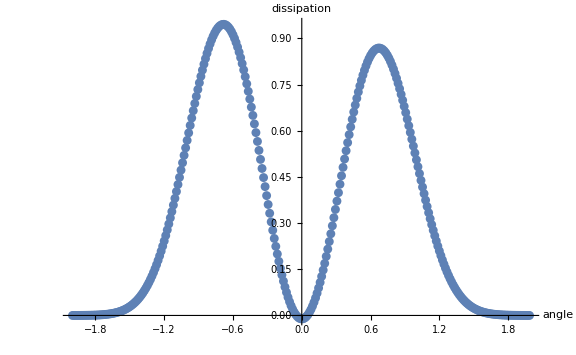

```mathematica
Dissipation={};
begining=-2;end=2;nstep=300;
ProgressIndicator[Dynamic[(δ-begining)/(end-begining)]]

β=0.02; δ=-2.36879β;
Q=Function[x,(-4 x^7+12 x^5 β^2+β^4-12 x^3 β^4+4 x β^6-4 x^6 δ^2+x^4 (-3+8 β δ (1+β δ))-2 x^2 β^2 (5+2 β δ (2+β δ)))/(4 (x^3-x β^2)^2)];zeros=NSolve[Q[x]==0,x];

ca=Function[t,(x/.zeros[[3]])+((x/.zeros[[1]])-(x/.zeros[[3]]))t];
caVal=Function[t,√Q[ca[t]]];
CA0=NIntegrate[ⅈ(caVal[t]ca'[t]),{t,0,1}];

da=Function[t,(x/.zeros[[5]])+((x/.zeros[[1]])-(x/.zeros[[5]]))t];
daVal=Function[t,√Q[da[t]]];
DA0=NIntegrate[ⅈ(daVal[t]da'[t]),{t,0,1}];

For[δ=begining,δ<end,δ+=(end-begining)/nstep,
Q=Function[x,(-4 x^7+12 x^5 β^2+β^4-12 x^3 β^4+4 x β^6-4 x^6 δ^2+x^4 (-3+8 β δ (1+β δ))-2 x^2 β^2 (5+2 β δ (2+β δ)))/(4 (x^3-x β^2)^2)];
zeros=NSolve[Q[x]==0,x];
cd=Function[t,(x/.zeros[[3]])+((x/.zeros[[5]])-(x/.zeros[[3]]))t];
cdVal=Function[t,√Q[cd[t]]];
CD=NIntegrate[ⅈ(cdVal[t]cd'[t]),{t,0,1}];

da=Function[t,(x/.zeros[[5]])+((x/.zeros[[1]])-(x/.zeros[[5]]))t];
daVal=Function[t,√Q[da[t]]];
DA=NIntegrate[ⅈ(daVal[t]da'[t]),{t,0,1}];
Amp=FullSimplify[S[-ⅈ].W[DA].S[-ⅈ].W[CD].S[(2+Exp[-2DA0])ⅈ*Exp[2CA0]].({{1}, {0}})];
Dissipation=Append[Dissipation,{δ,1-Abs[(Amp[[2]][[1]])/(Amp[[1]][[1]])]^2}];
]; Clear[Amp];
ListPlot[Dissipation,PlotRange->Full,AxesLabel->{angle,dissipation},ImageSize->Large]
```

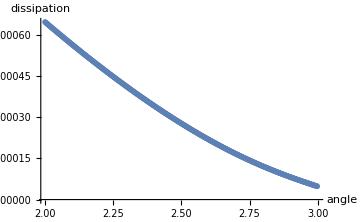

```mathematica
Dissipation={};
Stokes={};
begining=2;end=3;nstep=500;
ProgressIndicator[Dynamic[(δ-begining)/(end-begining)]]
χ=30;a78=-ⅈ;
For[δ=begining,δ<end,δ+=(end-begining)/nstep,
Q=Function[x,-(x+δ^2+3/(4 x^2))];
zeros=NSolve[Q[x]==0,x];
ca=Function[t,(x/.zeros[[3]])+((x/.zeros[[1]])-(x/.zeros[[3]]))t];
caVal=Function[t,√Q[ca[t]]];
CA=NIntegrate[ⅈ(caVal[t]ca'[t]),{t,0,1}];
(*===========================*)
sol = GeneralLinearAnizatropy[10^-5,0,χ,ArcSin[δ*χ^(-1/3)],π/2,{0,1}];
reflection = (sol[[5]][[2]])/(sol[[4]][[2]]);
a89=reflection-a78*Exp[-2CA];
Stokes=Append[Stokes,{δ,a89}];
Amp=FullSimplify[S[a89].W[CA].S[a78].({{1}, {0}})];
Dissipation=Append[Dissipation,{δ,1-Abs[(Amp[[2]][[1]])/(Amp[[1]][[1]])]^2}];
]; Clear[Amp];
ListPlot[Dissipation,PlotRange->Full,AxesLabel->{angle,dissipation}]
```

```mathematica
FindZeros[f_,{a_,b_,d_}]:= 
Module[{func=f, left = a, right = b, step = d},
$zeros={};
For[x = left, x < right, x += step,
AppendTo[$zeros,
SetAccuracy[z/.Quiet[FindRoot[func[z]==0,{z,x}]],5]];
];
Clear[x];
Sort[DeleteDuplicates[$zeros]]
]
```

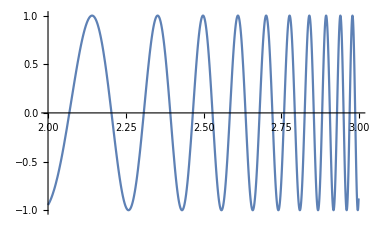

```mathematica
f=Interpolation[Table[{Stokes[[i,1]],Re[Stokes[[i,2]]]},{i,1,Length[Stokes]}]];
Plot[{f[x]},{x,2,Stokes[[Length[Stokes],1]]},PlotRange->{-1,1}]
```

{2.2039,2.3078,2.393,2.4655,2.5286,2.5846,2.6347,2.6799,2.7211,2.7587,2.7931,2.8248,2.854,2.881,2.9058,2.9287,2.9498,2.9692}

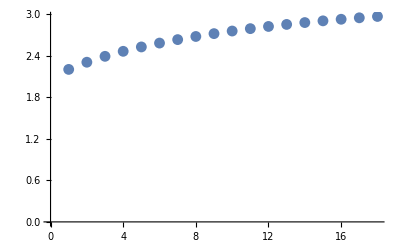

```mathematica
zz=FindZeros[f,{2.5,2.95,0.001}]
ListPlot[zz, AxesOrigin->{0,0}]
```

{a→0.1274,b→0.72128}

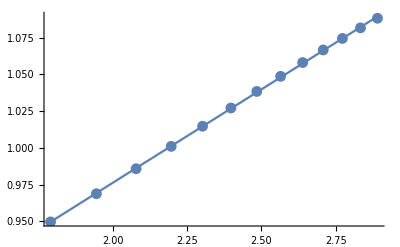

```mathematica
data=Table[{Log[i],Log[zz[[i]]]},{i,6,Length[zz]}];
model=Function[x,a x + b];
fit=FindFit[data,model[x],{a,b},x]
Show[{Plot[model[x]/.fit,{x,First[data][[1]],Last[data][[1]]}],ListPlot[data]}]
```

{a→1.428,b→7.455,c→11.161,d→0.14759}

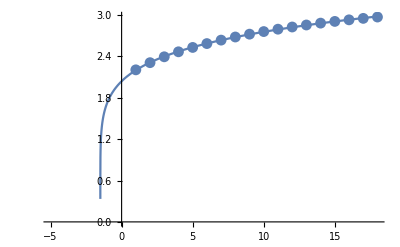

```mathematica
data=Table[{i,zz[[i]]},{i,1,Length[zz]}];
model=Function[x,a(b*x+c)^d];
fit=FindFit[data,model[x],{a,b,{c,6},{d,0.127403}},x]
Show[{Plot[model[x]/.fit,{x,-5,Last[data][[1]]},AxesOrigin->{0,0}],ListPlot[data]}]
```

{a→7.488,b→-3.108}

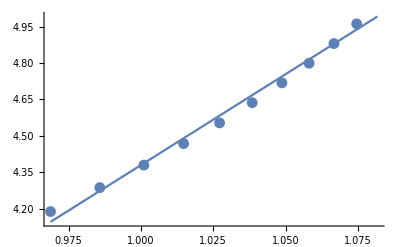

```mathematica
w=Table[{zz⟦i⟧,(2π)/(zz⟦i+1⟧-zz⟦i-1⟧)},{i,2,Length[zz]-1}];
data=Table[{Log[w⟦i,1⟧],Log[w⟦i,2⟧]},{i,6,Length[w]}];
model=Function[x,a x + b];
fit=FindFit[data,model[x],{a,b},x]
Show[{Plot[model[x]/.fit,{x,First[data][[1]],Last[data][[1]]}],ListPlot[data]}]
```

{a→6.54,b→0.0495,c→7.34}

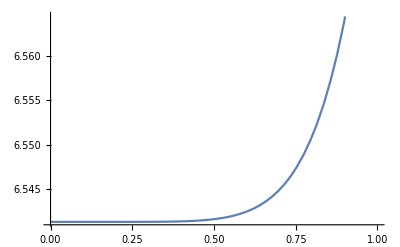

```mathematica
data=w;
model=Function[x,a +b*x^c];
fit=FindFit[data,model[x],{a,b,c},x]
Show[{Plot[model[x]/.fit,{x,0,1}],ListPlot[data]}]
```

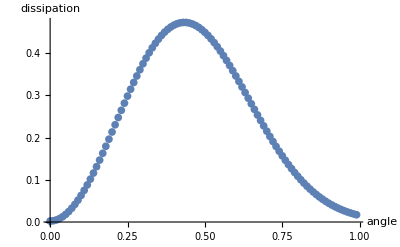

```mathematica
Dissipation={};
Stokes={};
begining=0;end=1;nstep=100;
ProgressIndicator[Dynamic[(δ-begining)/(end-begining)]]
χ=30;
For[δ=begining,δ<end,δ+=(end-begining)/nstep,
Q=Function[x,-(x+δ^2+3/(4 x^2))];
zeros=NSolve[Q[x]==0,x];
ca=Function[t,(x/.zeros[[3]])+((x/.zeros[[1]])-(x/.zeros[[3]]))t];
caVal=Function[t,√Q[ca[t]]];
CA=NIntegrate[ⅈ(caVal[t]ca'[t]),{t,0,1}];
(*===========================*)
sol = GeneralLinearAnizatropy[10^-5,0,χ,ArcSin[δ*χ^(-1/3)],π/2,{0,1}];
reflection = (sol[[5]][[2]])/(sol[[4]][[2]]);
a89=1;
a78=(reflection-a89)*Exp[2CA];
Stokes=Append[Stokes,{δ,a78}];
Amp=FullSimplify[S[a89].W[CA].S[a78].({{1}, {0}})];
Dissipation=Append[Dissipation,{δ,1-Abs[(Amp[[2]][[1]])/(Amp[[1]][[1]])]^2}];
]; Clear[Amp];
ListPlot[Dissipation,PlotRange->Full,AxesLabel->{angle,dissipation}]
```

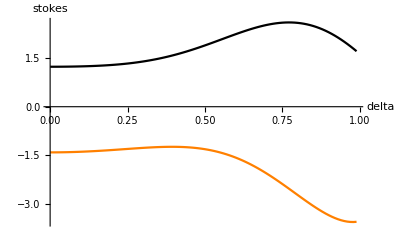

```mathematica
ListLinePlot[{Table[{Stokes[[i,1]],Re[Stokes[[i,2]]]},{i,1,Length[Stokes]}],
Table[{Stokes[[i,1]],Im[Stokes[[i,2]]]},{i,1,Length[Stokes]}]},PlotRange->Full,AxesLabel->{delta,stokes},PlotStyle->{Black,Orange}]
```

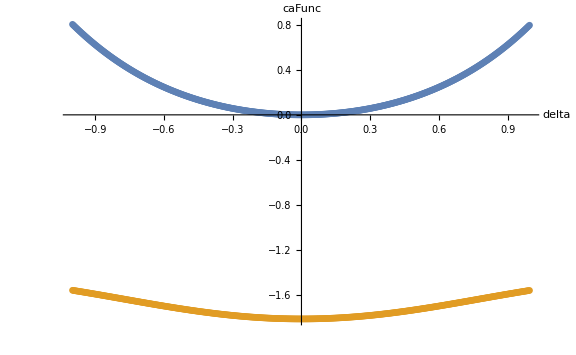

```mathematica
CAList={};
begining=-1;end=1;nstep=500;
ProgressIndicator[Dynamic[(δ-begining)/(end-begining)]]
For[δ=begining,δ<end,δ+=(end-begining)/nstep,
Q=Function[x,-(x+δ^2+3/(4 x^2))];
zeros=NSolve[Q[x]==0,x];
ca=Function[t,(x/.zeros[[3]])+((x/.zeros[[1]])-(x/.zeros[[3]]))t];
caVal=Function[t,√Q[ca[t]]];
CA=NIntegrate[ⅈ(caVal[t]ca'[t]),{t,0,1}];
CAList=Append[CAList,{δ,CA}];
];
ListPlot[{Re[CAList],Table[{CAList[[i,1]],Im[CAList[[i,2]]]},{i,1,Length[CAList]}]},PlotRange->Full,AxesLabel->{delta,caFunc},ImageSize->Large]
```

{a→0.791292,b→2.2774}

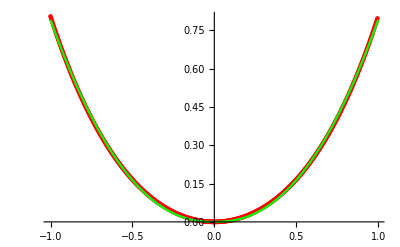

```mathematica
data=Table[{CAList⟦i,1⟧,Re[CAList⟦i,2⟧]},{i,260,Length[CAList]}];
model=Function[x,a Abs[x]^b];
fit=FindFit[data,model[x],{a,b},x]
ReCAFunc=Function[x,Evaluate[model[x]/.fit]];
Show[ListPlot[Table[{CAList⟦i,1⟧,Re[CAList⟦i,2⟧]},{i,1,Length[CAList]}],PlotStyle->Red],Plot[ReCAFunc[x],{x,-1,1},PlotStyle->{Green}]]
```

{a→-1.33216,b→-0.481988,c→0.661041}

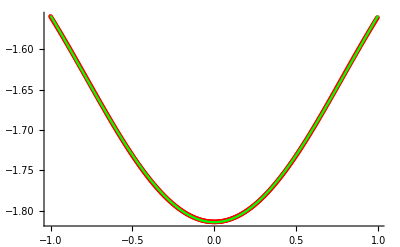

```mathematica
data=Table[{CAList⟦i,1⟧,Im[CAList⟦i,2⟧]},{i,1,Length[CAList]}];
model=Function[x,a+b ⅇ^(-x^2/(2c))];
fit=FindFit[data,model[x],{a,b,c},x]
ImCAFunc=Function[x,Evaluate[model[x]/.fit]];
Show[ListPlot[data,PlotStyle->Red],Plot[ImCAFunc[x],{x,-1,1},PlotStyle->{Green}]]
```

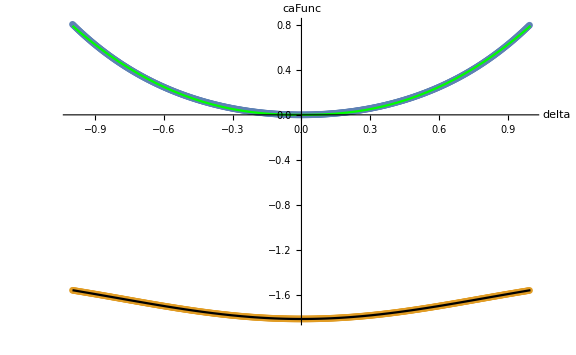

```mathematica
CAFunc=Function[x,ReCAFunc[x]+ⅈ ImCAFunc[x]];
Show[{ListPlot[{Re[CAList],Table[{CAList[[i,1]],Im[CAList[[i,2]]]},{i,1,Length[CAList]}]},PlotRange->Full,AxesLabel->{delta,caFunc},ImageSize->Large],Plot[{Re[CAFunc[x]],Im[CAFunc[x]]},{x,-1,1},PlotStyle->{Green,Black}]}]
```

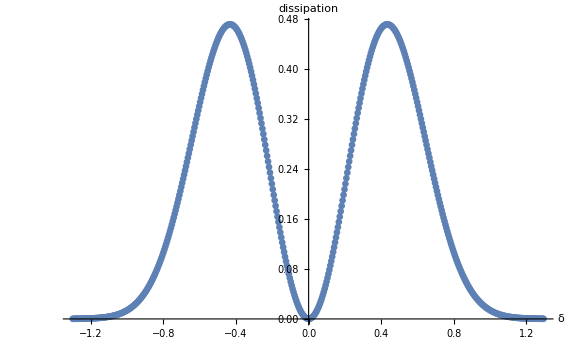

```mathematica
δDissipation={};
begining=-1.3;end=1.3;nstep=500;
ProgressIndicator[Dynamic[(δ-begining)/(end-begining)]]
For[δ=begining,δ<end,δ+=(end-begining)/nstep,
δDissipation=Append[δDissipation,{δ,GeneralLinearAnizatropy[0.000001,0,30,ArcSin[30^(-1/3)*δ],π/2,{0,1}][[7]]}];
]; Clear[δ,Amp];
ListPlot[δDissipation,PlotRange->Full,AxesLabel->{δ,dissipation},ImageSize->Large]
```

{ϕ→-5.67366,α→-3.83146}

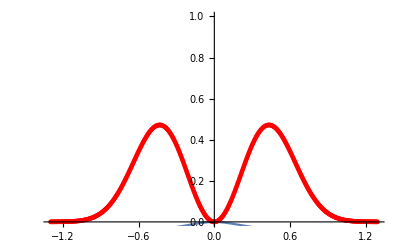

```mathematica
data=δDissipation;
(*model=Function[x,1-Abs[ⅇ^(ⅈ ϕ)+ρ ⅇ^(ⅈ s) ⅇ^(-2CAFunc[x])]^2];*)
model=Function[x,1-Abs[ⅇ^(ⅈ ϕ)+(ⅇ^(ⅈ α)-ⅇ^(ⅈ ϕ))ⅇ^(2CAFunc[0]) ⅇ^(-2CAFunc[x])]^2];
fit=FindFit[data,model[x],{ϕ,α},x,Method->NMinimize]
Show[{Plot[model[x]/.{α->0.9,ϕ->0},{x,-1,1}],ListPlot[δDissipation,PlotStyle->Red]},PlotRange->{0,1}]
```

```mathematica
model=Function[x,1-Abs[ⅇ^(ⅈ ϕ)+(ⅇ^(ⅈ α)-ⅇ^(ⅈ ϕ))ⅇ^(2CAFunc[0]) ⅇ^(-2CAFunc[x])]^2]; X0=0.43;V0=0.47;
fit=NSolve[model[X0]==V0&&model'[X0]==0&&-π<α<π&&-π<ϕ<π ,{α,ϕ}]
Show[Plot[model[x]/.fit,{x,-1,1}],ListPlot[δDissipation,PlotStyle->Red]]
```

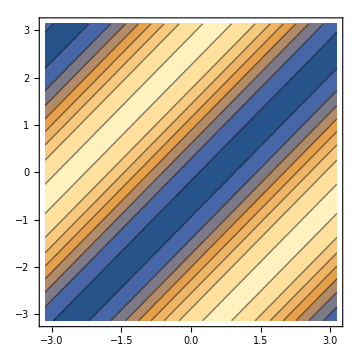

```mathematica
ContourPlot[model[X0]-V0,{α,-π,π},{ϕ,-π,π}]
```

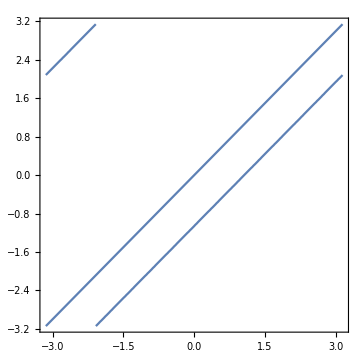

```mathematica
ContourPlot[(Evaluate[D[ComplexExpand[model[x]],x]]/.x->X0)==0,{α,-π,π},{ϕ,-π,π}]
```

```mathematica
model[X0]/.{α->-2.6,ϕ->0}
```

0.68829

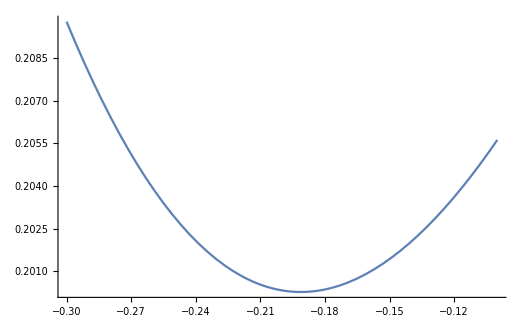

```mathematica
Plot[((Evaluate[D[ComplexExpand[model[x]],x]]/.x->X0)^2+(model[X0]-V0)^2)/.ϕ->0,{α,-0.3,-0.1}]
```